```mathematica
data = Import["/Users/philliphuang/Desktop/d0.xlsx"]
```

{{{128.,0.000184},{256.,0.000452},{512.,0.001642},{1024.,0.004165},{2048.,0.008332},{4096.,0.025912},{8192.,0.068664},{16384.,0.16413},{32768.,0.380224},{65536.,0.829719},{131072.,1.81754}}}

```mathematica
model=LinearModelFit[data[[1]],n,n]
```

```mathematica
FittedModel[-0.02838674460300038+0.000013790059349936661 n]
```

FittedModel[-0.0283867+0.0000137901 n]

```mathematica
model["BestFit"]
```

-0.0283867+0.0000137901 n

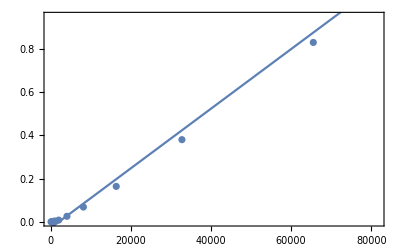

```mathematica
Show[ListPlot[data],Plot[model[n],{n,0,150000}],Frame->True]
```

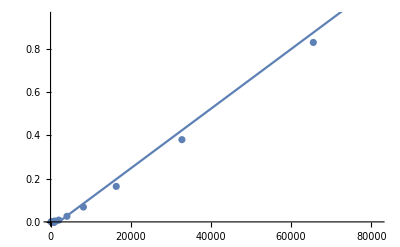

```mathematica
Show[ListPlot[data],Plot[model["BestFit"],{n,0,150000}]]
```

```mathematica
Plot[m["BestFit"],{x,0,150000}]
```

-Graphics-